# First Order SE in τ p=0

```mathematica
SetDirectory["/home/h/H.Guertner/theorie/BEC_Polaron/Mathematica/"];
<<params.mx;
ResetDirectory[];
p = 0;
μ = -7;(*Import["DiagMC_BEC.json", {"Data", "Chemical_Potential"} ];*)
α = Import["DiagMC_BEC.json", {"Data", "Alpha"} ];
mr = Import["DiagMC_BEC.json", {"Data", "Impurity_Mass"} ];
qc = Import["DiagMC_BEC.json", {"Data", "Q_Cutoff"} ];
taus = Import["data/zero_order", "table"][[All,1]];
FP= False;(*Import["DiagMC_BEC.json", {"Data", "Froehlich_Polaron"} ];*)
```

## SE in iw analytical

```mathematica
f2[q_,w_, w1_]:=-(4*Pi)/(2*Pi)^4 *q^2*If[FP,vq2FP[q]*g0pwFPmu[-q,I w - I w1,0]*dqwFP[I w1,0], vq2[q]*g0pwmu[-q,I w - I w1,0]*dqw[q,I w1,0]];
g2[q_,w_] := Integrate[f2[q,w,w1], {w1,-Infinity, Infinity}]
h2[q_,w_]:=2* Pi* I*Residue[f2[q,w, w1], {w1, w+ If[FP,I q^2/2, I q^2/2/mr*Sqrt[2]] - I μ}];
h2[q,w];
(*f2[q,w,w1]
Simplify[f2[q,w,w+ If[FP,I q^2/2, I q^2/2/mr*Sqrt[2]] - I μ]]
Integrate[f2[q,w,w1], {w1,-Infinity, Infinity}]
(*Integrate[g2[q,w]/2/Pi*Exp[-I w t], {w,-Infinity, Infinity}]*)
2* Pi* I*Residue[f2[q,w,w1], {w1, w+ If[FP,I q^2/2, I q^2/2/mr*Sqrt[2]] - I μ}]
2* Pi *I* Residue[h2[q,w], {w, - I q^2/2 + I μ - I wq[q]}]*)
```

```mathematica
(*Plot[Re[h2[1,w]/2/Pi], {w,-wintmax,wintmax}, PlotPoints->10, MaxRecursion->3]
Plot[Im[h2[1,w]/2/Pi], {w,-wintmax,wintmax}, PlotPoints->10, MaxRecursion->3]*)
```

```mathematica
wc=10^7;
sew[t_]:=2*Re[NIntegrate[h2[q,w]/2/Pi*Exp[-I w *t],{q,0, qc},{w,0, wc},AccuracyGoal->5]];
```

```mathematica
(*sewtest[t_, wc_]:=2*Re[NIntegrate[h2[q,w]/2/Pi*Exp[-I w *t],{q,0, qc},{w,0, wc},AccuracyGoal->5]];
LogLinearPlot[sewtest[1,wc], {wc,10,100000000}, MaxRecursion->2, PlotPoints->10]*)
```

## t Integral

```mathematica
f[q_,τ_]:=(4*Pi)/(2*Pi)^3 *q^2*If[FP,vq2FP[q]*g0FP[-q,0,τ]*dqFP[0,τ], vq2[q]*g0[-q,0,τ]*dq[q,0,τ]];
```

## q Integral

```mathematica
se[τ_]:=NIntegrate[f[q, τ],{q,0, qc},AccuracyGoal->1000];
```

## Check qc Convergence

### First Order

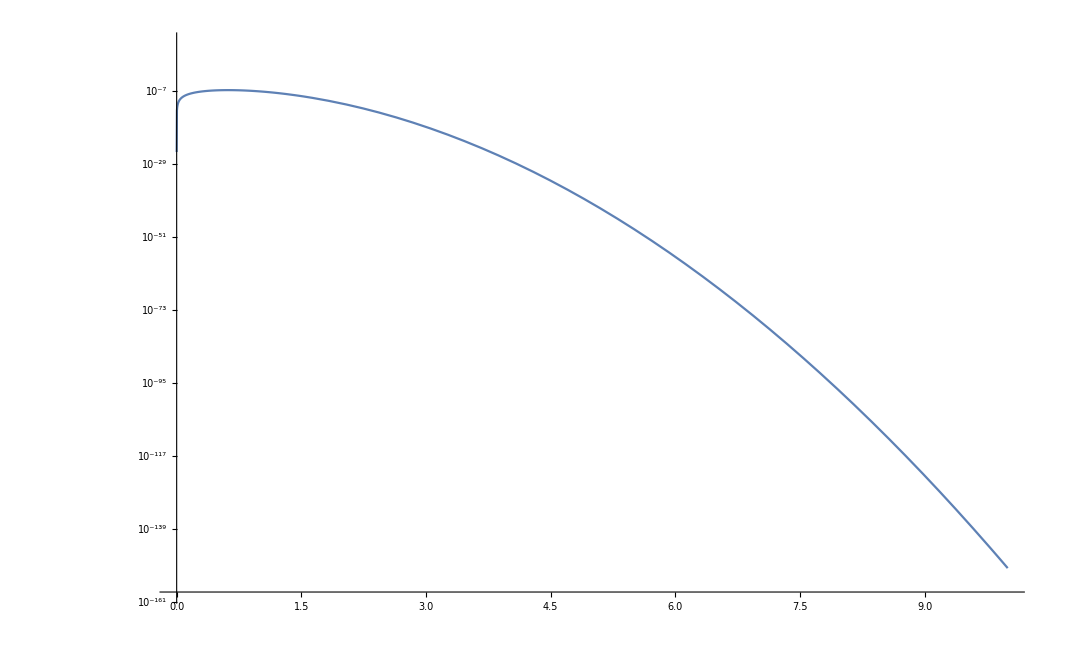

```mathematica
α = 0.002;
fic[q_,τ_]:=(4*Pi)/(2*Pi)^3 *q^2*vq2[q]*g0[-q,0,τ]*dq[q,0,τ];
seqc[τ_, qc_]:=NIntegrate[fic[q, τ],{q,0, qc},AccuracyGoal->100];
(*LogLogPlot[seqc[1, qc], {qc,10, 1000}, PlotPoints->10, MaxRecursion->10]*)
LogPlot[fic[q,1],{q,0,10}]
```

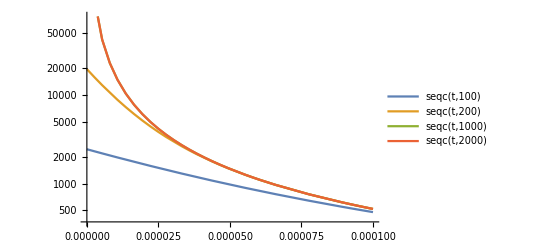

```mathematica
α = 0.002;
LogPlot[{seqc[t, 100], seqc[t, 200], seqc[t, 1000], seqc[t, 2000]}, {t,0, 0.0001}, PlotPoints->10, MaxRecursion->2, PlotLegends->"Expressions"]
```

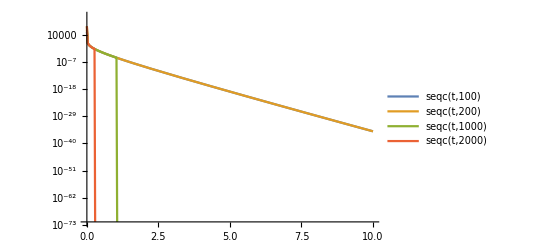

```mathematica
α = 0.1;
LogPlot[{seqc[t, 100], seqc[t, 200], seqc[t, 1000], seqc[t, 2000]}, {t,0, 10}, PlotPoints->10, MaxRecursion->5, PlotLegends->"Expressions"]
```

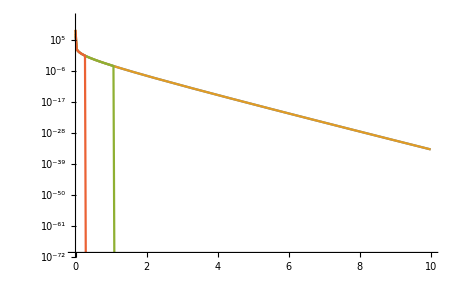

```mathematica
α = 2;
LogPlot[{seqc[t, 100], seqc[t, 200], seqc[t, 1000], seqc[t, 2000]}, {t,0, 10}, PlotPoints->10, MaxRecursion->5]
```

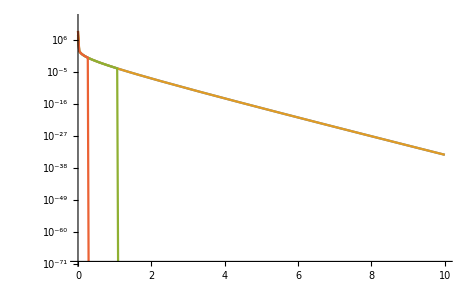

```mathematica
α = 5;
LogPlot[{seqc[t, 100], seqc[t, 200], seqc[t, 1000], seqc[t, 2000]}, {t,0, 10}, PlotPoints->10, MaxRecursion->5]
```

### Second Order Rainbow

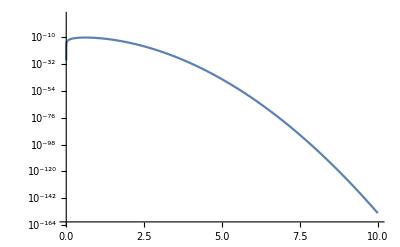

```mathematica
α = 0.002;
IntegBEC[q1_,q2_,τ_,τ1_, τ2_, ctheta_] := vq2[q1]*vq2[q2]*g0[q1,0,τ1]*dq[q1,0,τ]*g0cos[q1,q2,τ1,τ2, ctheta]*dq[q2,τ1,τ2]*g0[q1,τ2,τ];
f[q1_,q2_,τ_,τ1_, τ2_, ctheta_]:=4*Pi*2*Pi/(2*Pi)^6 *q1^2*q2^2* IntegBEC[q1,q2,τ,τ1, τ2, ctheta];
g[q1_,q2_, τ_,τ2_,ctheta_] := Integrate[f[q1,q2,τ,τ1,τ2,ctheta],  {τ1,0,τ2}];
fic2[q1_,q2_, τ_, ctheta_] := Integrate[g[q1,q2,τ,τ2, ctheta],  {τ2,0,τ}];
seqc2[τ_, qc_]:=NIntegrate[fic2[q1, q2, τ, ctheta],{q1,0, qc}, {q2,0, qc}, {ctheta, -1,1}, AccuracyGoal->100];
LogPlot[fic2[q,1, 1,0],{q,0,10}]
```

## Comparison to Analytical Result

```mathematica
(*se[1]
sew[1]
Plot[{-sew[t], se[t]}, {t,0,3}, MaxRecursion->1, PlotPoints->10]*)
```

## Export

```mathematica
(*sedata = Table[{t, se[t]}, {t, taus}];*)
```

```mathematica
(*Export["data/SE/mat_1st_se", sedata, "Table"];*)
```